# Лабораторная работа №2

## Глёза Егор, группа 221701 Вариант 1

## 1.Создать таблицу значений функции f(x) разбив отрезок [0, 6] на n равных частей точками x_i (i = OverBar[0,n]). Для полученной таблично заданной в равноотстоящих узлах функции f(x) , выполнить следующие действия при n = 6 и n = 10:

```mathematica
f[x_]:=5Exp[-1/18 x^2+1/3 x-1/2]-2Sin[√x];
a=0;
b=6;
GraphicSize={x, a,2b};
```

## Задача при n = 6

```mathematica
n=6;
```

### a) построить интерполяционный многочлен Лагранжа L_n(x), проиллюстрировать графически;

```mathematica
ClearAll;
```

Зададим функцию построения интерполяционного многочлена Лагранжа:

```mathematica
L[X_,Y_,x_,n_]:= ∑_i^(n+1) (Y⟦i⟧ ∏_j^(n+1) If[i≠j,x-X⟦j⟧,1])/(∏_j^(n+1) If[i≠j,X⟦i⟧-X⟦j⟧,1]);
```

Зададим таблицы значений X и Y:

```mathematica
X = Table[i, {i,a,b,(a+b)/n}];
Y = Table[f[x]//N, {x,X}];
```

Построим интерполяционный многочлен Лагранжа с помощью функции:

```mathematica
Ln[x_]=L[X,Y,x,n]//Simplify
```

3.03265-2.28305 x+2.35579 x^2-0.96622 x^3+0.203065 x^4-0.0225344 x^5+0.00103677 x^6

Построим графики:

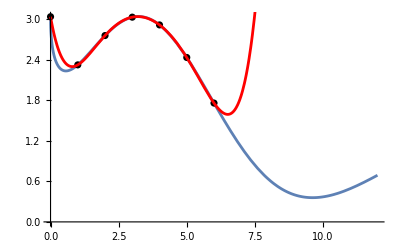

```mathematica
gr1=Plot[f[x],GraphicSize];
gr2=ListPlot[Table[{i, f[i]}, {i, a, b, (b-a)/n}]//N,PlotStyle->{Black}];
gr3 = Plot[Ln[x],GraphicSize, PlotStyle->{Red}];
Show[gr1,gr2,gr3]
```

### б) создать таблицу разделенных разностей функции f (x) по точкам (x_i,f(x_i)),i=OverBar[0,n];

Составим таблицу значений функции f(x) в равноотстоящих узлах:

```mathematica
data = Table[{i, f[i]}, {i, a, b, (b-a)/n}]//N;
```

Создадим массив dif размера (n+1)×(n+1) с начальными индексами (0, 0), в котором будем хранить конечные разности.

```mathematica
Array[dif, {n+1,n+1},{0,0}];
```

Определим элементы массива dif, которые соответствуют пустым клеткам таблицы

```mathematica
For[k=1,k<=n,k++,
For[i=n,i>=n-k,i--,
dif[i,k]=""
]
];
```

Заполним элементы первого столбца массива dif[i,0] – конечные разности нулевого порядка:

```mathematica
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
```

Затем заполним элементы массива dif с конечными разностями остальных порядков:

```mathematica
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]
]
];
```

Выведем построенную таблицу конечных разностей:

```mathematica
tab = Array[dif,{n+1,n+1}, {0,0}];
PaddedForm[TableForm[tab], {6,5}]
```

3.03265 | -0.71191 |  1.14543 | -1.30727 |  1.08268 | -0.83794 |  0.74647
 2.32075 |  0.43352 | -0.16184 | -0.22459 |  0.24474 | -0.09147 | 
 2.75427 |  0.27168 | -0.38643 |  0.02016 |  0.15328 |  | 
 3.02595 | -0.11474 | -0.36627 |  0.17343 |  |  | 
 2.91120 | -0.48101 | -0.19284 |  |  |  | 
 2.43019 | -0.67385 |  |  |  |  | 
 1.75634 |  |  |  |  |  |

### в) построить первый или второй интерполяционный многочлен Ньютона Pn(x) , проиллюстрировать графически;

Построим первый интерполяционный многочлен Ньютона Pn1:

```mathematica
t=n(x-a)/(b-a);
Pn1[x_]=dif[0,0];
p[t_]=1;
For[k=1,k<=n,k++,
p[t_]=p[t](t-k+1);
Pn1[x_]=Pn1[x]+dif[0,k]/(k!)p[t];
];
Pn1[x]
```

3.03265-0.711908 x+0.572714 (-1+x) x-0.217878 (-2+x) (-1+x) x+0.0451117 (-3+x) (-2+x) (-1+x) x-0.00698283 (-4+x) (-3+x) (-2+x) (-1+x) x+0.00103677 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x

Упростим вид многочлена Pn1:

```mathematica
Pn1[x_]=Simplify[Pn1[x]]
```

3.03265-2.28305 x+2.35579 x^2-0.96622 x^3+0.203065 x^4-0.0225344 x^5+0.00103677 x^6

Построим графики:

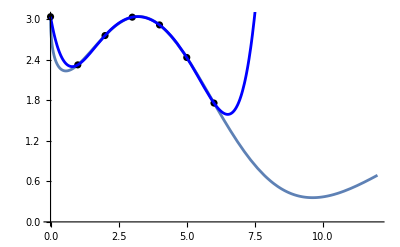

```mathematica
gr4 = Plot[Pn1[x],GraphicSize, PlotStyle->{Blue}];
Show[gr1,gr2,gr4]
```

### г) построить интерполяционный многочлен Ньютона Np_n(x) с помощью функции InterpolatingPolynomial пакета Mathematica, проиллюстрировать графически;

Построим интерполяционный многочлен Ньютона и упростим его вид:

```mathematica
Np6[x_]=InterpolatingPolynomial[data,x]//Simplify
```

3.03265-2.28305 x+2.35579 x^2-0.96622 x^3+0.203065 x^4-0.0225344 x^5+0.00103677 x^6

Построим графики:

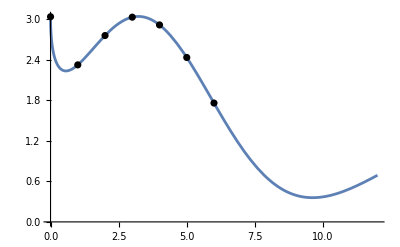

```mathematica
gr5=Plot[Np[x],GraphicSize,PlotStyle->{Green}];
Show[gr1,gr2,gr5]
```

### д) вычислить значения функции f(x) и всех построенных интерполяционных многочленов L_n(x), P_n(x), Np_n(x) в точке x = 2,4316;

```mathematica
f[2.4316]
Ln[2.4316]
Pn1[2.4316]
Np6[2.4316]
```

2.91119

2.91645

2.91645

2.91645

### е) построить график погрешности интерполирования многочленом Ньютона R_n(x)=|f(x)-Np_n(x)| на отрезке [0, 6], найти максимум погрешности R_n(x) на отрезке [0, 6] с помощью функции FindMaximum пакета Mathematica;

Зададим функцию R_n(x):

```mathematica
Rn6[x_]=Abs[f[x]-Np6[x]];
```

Найдём максимум погрешности R_n(x) на отрезке [0, 6]:

```mathematica
FindMaximum[Rn6[x],{x,0,6}]
```

{0.316287,{x→0.114284}}

Построим график:

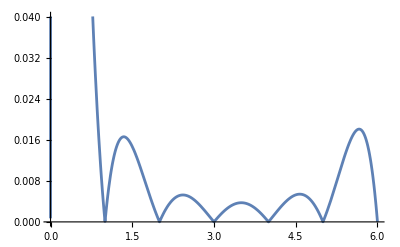

```mathematica
grn6=Plot[Rn6[x],{x,0,6}]
```

## Задача при n = 10

```mathematica
n=10
```

10

### a) построить интерполяционный многочлен Лагранжа L_n(x), проиллюстрировать графически;

```mathematica
ClearAll;
```

Зададим таблицы значений X и Y:

```mathematica
X = Table[i, {i,a,b,(a+b)/n}];
Y = Table[f[x]//N, {x,X}];
```

Построим интерполяционный многочлен Лагранжа с помощью функции:

```mathematica
Ln[x_]=L[X,Y,x,n]//Simplify
```

3.03265-3.77992 x+6.92081 x^2-6.78008 x^3+4.34104 x^4-1.8606 x^5+0.533848 x^6-0.101229 x^7+0.0121725 x^8-0.000840399 x^9+0.0000253567 x^10

Построим графики:

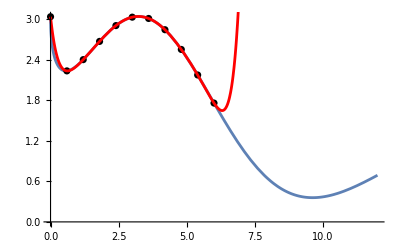

```mathematica
gr1=Plot[f[x],GraphicSize];
gr2=ListPlot[Table[{i, f[i]}, {i, a, b, (b-a)/n}]//N,PlotStyle->{Black}];
gr3 = Plot[Ln[x],GraphicSize, PlotStyle->{Red}];
Show[gr1,gr2,gr3]
```

### б) создать таблицу разделенных разностей функции f (x) по точкам (x_i,f(x_i)),i=OverBar[0,n];

Составим таблицу значений функции f(x) в равноотстоящих узлах:

```mathematica
data = Table[{i, f[i]}, {i, a, b, (b-a)/n}]//N;
```

Создадим массив dif размера (n+1)×(n+1) с начальными индексами (0, 0), в котором будем хранить конечные разности.

```mathematica
Array[dif, {n+1,n+1},{0,0}];
```

Определим элементы массива dif, которые соответствуют пустым клеткам таблицы

```mathematica
For[k=1,k<=n,k++,
For[i=n,i>=n-k,i--,
dif[i,k]=""
]
];
```

Заполним элементы первого столбца массива dif[i,0] – конечные разности нулевого порядка:

```mathematica
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
```

Затем заполним элементы массива dif с конечными разностями остальных порядков:

```mathematica
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]
]
];
```

Выведем построенную таблицу конечных разностей:

```mathematica
tab = Array[dif,{n+1,n+1}, {0,0}];
PaddedForm[TableForm[tab], {2,2}]
```

3.00 | -0.80 |  0.97 | -0.86 |  0.72 | -0.66 |  0.63 | -0.61 |  0.59 | -0.57 |  0.56
 2.20 |  0.17 |  0.10 | -0.14 |  0.07 | -0.03 |  0.02 | -0.02 |  0.02 | -0.01 | 
 2.40 |  0.27 | -0.04 | -0.07 |  0.04 | -0.01 |  0.00 | -0.00 |  0.00 |  | 
 2.70 |  0.23 | -0.11 | -0.03 |  0.03 | -0.01 | -0.00 |  0.00 |  |  | 
 2.90 |  0.12 | -0.14 | -0.00 |  0.03 | -0.01 | -0.00 |  |  |  | 
 3.00 | -0.02 | -0.15 |  0.02 |  0.02 | -0.01 |  |  |  |  | 
 3.00 | -0.17 | -0.13 |  0.04 |  0.01 |  |  |  |  |  | 
 2.80 | -0.29 | -0.09 |  0.05 |  |  |  |  |  |  | 
 2.50 | -0.38 | -0.04 |  |  |  |  |  |  |  | 
 2.20 | -0.42 |  |  |  |  |  |  |  |  | 
 1.80 |  |  |  |  |  |  |  |  |  |

### в) построить первый или второй интерполяционный многочлен Ньютона Pn(x) , проиллюстрировать графически;

Построим первый интерполяционный многочлен Ньютона Pn1:

```mathematica
t=n(x-a)/(b-a);
Pn1[x_]=dif[0,0];
p[t_]=1;
For[k=1,k<=n,k++,
p[t_]=p[t](t-k+1);
Pn1[x_]=Pn1[x]+dif[0,k]/(k!)p[t];
];
Pn1[x]
```

3.03265-1.33461 x+0.805801 x (-1+(5 x)/3)-0.239828 x (-2+(5 x)/3) (-1+(5 x)/3)+0.0502513 x (-3+(5 x)/3) (-2+(5 x)/3) (-1+(5 x)/3)-0.00912199 x (-4+(5 x)/3) (-3+(5 x)/3) (-2+(5 x)/3) (-1+(5 x)/3)+0.00145427 x (-5+(5 x)/3) (-4+(5 x)/3) (-3+(5 x)/3) (-2+(5 x)/3) (-1+(5 x)/3)-0.00020066 x (-6+(5 x)/3) (-5+(5 x)/3) (-4+(5 x)/3) (-3+(5 x)/3) (-2+(5 x)/3) (-1+(5 x)/3)+0.0000242478 x (-7+(5 x)/3) (-6+(5 x)/3) (-5+(5 x)/3) (-4+(5 x)/3) (-3+(5 x)/3) (-2+(5 x)/3) (-1+(5 x)/3)-2.61629×10^-6 x (-8+(5 x)/3) (-7+(5 x)/3) (-6+(5 x)/3) (-5+(5 x)/3) (-4+(5 x)/3) (-3+(5 x)/3) (-2+(5 x)/3) (-1+(5 x)/3)+2.55537×10^-7 x (-9+(5 x)/3) (-8+(5 x)/3) (-7+(5 x)/3) (-6+(5 x)/3) (-5+(5 x)/3) (-4+(5 x)/3) (-3+(5 x)/3) (-2+(5 x)/3) (-1+(5 x)/3)

Упростим вид многочлена Pn1:

```mathematica
Pn1[x_]=Simplify[Pn1[x]]
```

3.03265-3.77992 x+6.92081 x^2-6.78008 x^3+4.34104 x^4-1.8606 x^5+0.533848 x^6-0.101229 x^7+0.0121725 x^8-0.000840399 x^9+0.0000253567 x^10

Построим графики:

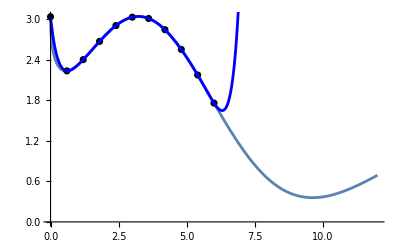

```mathematica
gr4 = Plot[Pn1[x],GraphicSize, PlotStyle->{Blue}];
Show[gr1,gr2,gr4]
```

### г) построить интерполяционный многочлен Ньютона Np_n(x) с помощью функции InterpolatingPolynomial пакета Mathematica, проиллюстрировать графически;

Построим интерполяционный многочлен Ньютона и упростим его вид:

```mathematica
Np10[x_]=InterpolatingPolynomial[data,x]//Simplify
```

3.03265-3.77992 x+6.92081 x^2-6.78008 x^3+4.34104 x^4-1.8606 x^5+0.533848 x^6-0.101229 x^7+0.0121725 x^8-0.000840399 x^9+0.0000253567 x^10

Построим графики:

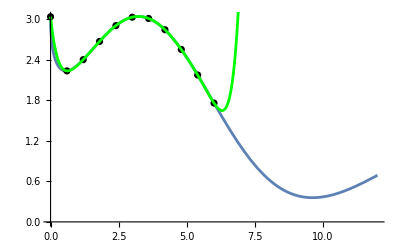

```mathematica
gr5=Plot[Np10[x],GraphicSize,PlotStyle->{Green}];
Show[gr1,gr2,gr5]
```

### д) вычислить значения функции f(x) и всех построенных интерполяционных многочленов L_n(x), P_n(x), Np_n(x) в точке x = 2,4316;

```mathematica
f[2.4316]
Ln[2.4316]
Pn1[2.4316]
Np10[2.4316]
```

2.91119

2.91122

2.91122

2.91122

### е) построить график погрешности интерполирования многочленом Ньютона R_n(x)=|f(x)-Np_n(x)| на отрезке [0, 6], найти максимум погрешности R_n(x) на отрезке [0, 6] с помощью функции FindMaximum пакета Mathematica;

Зададим функцию R_n(x):

```mathematica
Rn10[x_]=Abs[f[x]-Np10[x]];
```

```mathematica
FindMaximum[Rn10[x],{x,0,6}]
```

{0.221177,{x→0.0572043}}

Построим график:

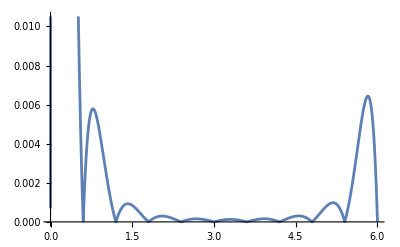

```mathematica
grn10=Plot[Rn10[x],{x,0,6}]
```

## ж) исследовать зависимость погрешности интерполирования R_n(x) от числа узлов интерполяции.

Выведем графики R_n(x) при n = 6 и n = 10:

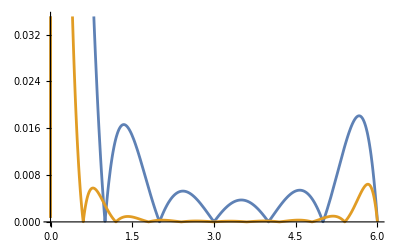

```mathematica
Plot[{Rn6[x], Rn10[x]}, {x,0,6}]
```

Из графика видно, что при n = 10 погрешность меньше, чем при n = 6.

## 2. Создать таблицу значений функции f(x), разбив отрезок [6, 0] на n частей неравноотстоящими точками x_i вида x_i=(a+b)/2+(b-a)/2 t_i, где t_i – корни многочлена Чебышёва T_(n+1)(t)(i=OverBar[0,i]). Для полученной таблично заданной функции f(x), выполнить следующие действия при n = 6 и n = 10:

## n = 6

```mathematica
n=6;
```

### а) создать таблицу разделенных разностей функции f(x) по точкам

Вычислим корни многочлена Чебышёва T_(n+1)(t)(i=OverBar[0,i])

```mathematica
Clear[t];
t =Table[Cos[(Pi(2r+1))/(2n)]//N,{r,0,n-1}];
```

Создадим таблицу разделённых разностей

```mathematica
x[i_]:=(a+b)/2+(b-a)/2 t[[i]];
ndata=Table[{x[i],f[x[i]]},{i,n}];
ndata //TableForm
```

5.89778 | 1.82765
5.12132 | 2.35436
3.77646 | 2.97248
2.22354 | 2.84164
0.87868 | 2.28198
0.102223 | 2.50734

### б) построить интерполяционный многочлен Ньютона Pnr_n(x) для неравноотстоящих узлов, проиллюстрировать графически

```mathematica
Prn6[x_]=InterpolatingPolynomial[ndata,x]//Simplify
```

2.6155-1.17731 x+1.20483 x^2-0.378041 x^3+0.047587 x^4-0.0022107 x^5

Построим графики

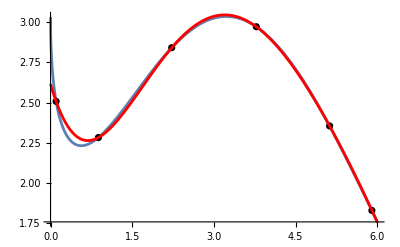

```mathematica
Show[Plot[f[x],{x,0,6}], ListPlot[ndata, PlotStyle->{Black}], Plot[Prn6[x],{x,0,6},PlotStyle->{Red}]]
```

### в) построить интерполирующую функцию Intf_n(x) с помощью функции Interpolation пакета Mathematica, проиллюстрировать графически;

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

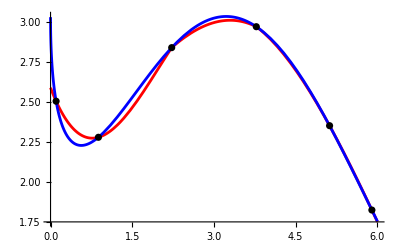

```mathematica
Intf[x_]=Interpolation[ndata,x];
Show[Plot[{Intf[x], f[x]},{x,0,6}, PlotStyle->{Red, Blue}],ListPlot[ndata, PlotStyle->{Black}]]
```

### г) вычислить значения функции f(x) и построенных интерполяционных многочленов Prn_n(x) и Intf_n(x) в точке x=2.4216;

```mathematica
f[2.4216]
Prn6[2.4216]
Intf[2.4216]
```

2.90814

2.91376

2.8962

### д) найти максимумы абсолютных погрешностей интерполирования функции f(x)многочленом Ньютона Prn_n(x) и функцией Intf_n(x) на отрезке [6, 0] с помощью функции FindMaximum пакета Mathematica.

```mathematica
R6[x_]=Abs[f[x]-Prn6[x]];
R2[x_]=Abs[f[x]-Intf[x]];
FindMaximum[{R6[x],a <=x<=b}, {x,0.1}]
FindMaximum[{R2[x],a <=x<=b}, {x,3.4}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.411533,{x→7.95143×10^-6}}

{0.027804,{x→2.98138}}

## n = 10

```mathematica
n=10;
```

### а) создать таблицу разделенных разностей функции f(x) по точкам

Вычислим корни многочлена Чебышёва T_(n+1)(t)(i=OverBar[0,i])

```mathematica
Clear[t];
t =Table[Cos[(Pi(2r+1))/(2n)]//N,{r,0,n-1}];
```

Создадим таблицу разделённых разностей

```mathematica
x[i_]:=(a+b)/2+(b-a)/2 t[[i]];
ndata=Table[{x[i],f[x[i]]},{i,n}];
ndata //TableForm
```

5.96307 | 1.78208
5.67302 | 1.98432
5.12132 | 2.35436
4.36197 | 2.77251
3.4693 | 3.02374
2.5307 | 2.93959
1.63803 | 2.59444
0.87868 | 2.28198
0.32698 | 2.27952
0.036935 | 2.68798

### б) построить интерполяционный многочлен Ньютона Pnr_n(x) для неравноотстоящих узлов, проиллюстрировать графически

```mathematica
Prn10[x_]=InterpolatingPolynomial[ndata,x]//Simplify
```

2.78538-2.82316 x+5.21067 x^2-4.8042 x^3+2.76538 x^4-1.01134 x^5+0.232371 x^6-0.0324675 x^7+0.00252085 x^8-0.0000833981 x^9

Построим графики

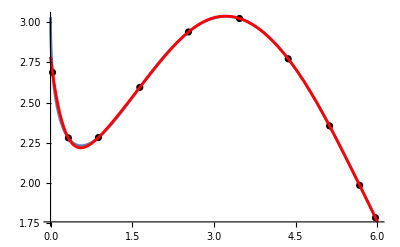

```mathematica
Show[Plot[f[x],{x,0,6}], ListPlot[ndata, PlotStyle->{Black}], Plot[Prn10[x],{x,0,6},PlotStyle->{Red}]]
```

### в) построить интерполирующую функцию Intf_n(x) с помощью функции Interpolation пакета Mathematica, проиллюстрировать графически;

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

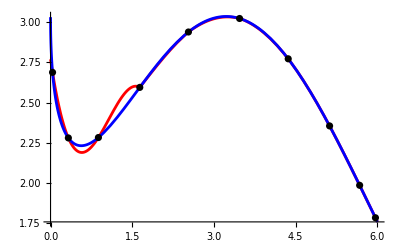

```mathematica
Intf[x_]=Interpolation[ndata,x];
Show[Plot[{Intf[x], f[x]},{x,0,6}, PlotStyle->{Red, Blue}],ListPlot[ndata, PlotStyle->{Black}]]
```

### г) вычислить значения функции f(x) и построенных интерполяционных многочленов Prn_n(x) и Intf_n(x) в точке x=2.4216;

```mathematica
f[2.4216]
Prn10[2.4216]
Intf[2.4216]
```

2.90814

2.90681

2.90619

### д) найти максимумы абсолютных погрешностей интерполирования функции f(x)многочленом Ньютона Prn_n(x) и функцией Intf_n(x) на отрезке [6, 0] с помощью функции FindMaximum пакета Mathematica.

```mathematica
R10[x_]=Abs[f[x]-Prn10[x]];
R2[x_]=Abs[f[x]-Intf[x]];
FindMaximum[{R10[x],a<=x<=b}, {x,0.1}]
FindMaximum[{R2[x],a<=x<=b}, {x,3.4}]
```

{0.0393105,{x→0.110607}}

{0.0041028,{x→2.99452}}

## 3. Сравнить результаты заданий 1 и 2 для равноотстоящих и неравноотстоящих узлов и сделать выводы о зависимости погрешности интерполирования от числа узлов и их расположения на отрезке.

Построим графики

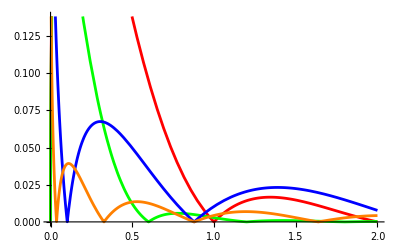

```mathematica
Show[Plot[{Rn6[x], Rn10[x],R6[x], R10[x]},{x,0,2}, PlotStyle->{Red,Green,Blue,Orange}]]
```

## 4. Используя таблицу значений функции f(x) в равноотстоящих точках отрезка [6, 0], полученной в задании 1 при n = 10, выполнить следующие действия:

### б) выполнить интерполяцию сплайном Sf(x) с помощью функции Interpolation[data,Method->“Spline”], проиллюстрировать графически;

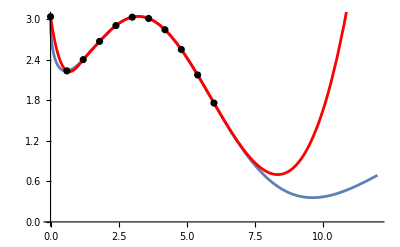

```mathematica
Sf=Interpolation[data,Method->"Spline"];
Show[gr1,Plot[Sf[x],{x,0,12},PlotStyle->{Red}],gr2]
```

### г) вычислить значения функции f(x) и построенного интерполяционного сплайна Sf(x) в точке x = 2.4216.

```mathematica
f[2.4216]
Sf[2.4216]
```

2.90814

2.90826

## 5. Используя таблицу значений функции f(x) в равноотстоящих точках отрезка [6, 0], полученной в задании 1 при n = 10, выполнить следующие действия:

### а) аппроксимировать с помощью метода наименьших квадратов функцию f(x) многочленом первой степени Q_1(x), проиллюстрировать графически;

2.85837-0.0866874 x

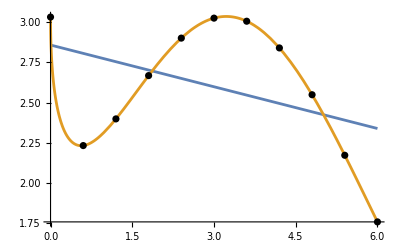

```mathematica
r=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) X⟦j⟧^(i+k)],{i,0,1}],{k,0,1}],Table[If[i==0,∑_(j=1)^(n+1) Y⟦j⟧,∑_(j=1)^(n+1) Y⟦j⟧ X⟦j⟧^i],{i,0,1}]];
Q1[x_]=r.{1,x}
Show[Plot[{Q1[x], f[x]},{x,0,6}],ListPlot[data, PlotStyle->{Black}]]
```

### б) аппроксимировать с помощью метода наименьших квадратов функцию f(x) многочленом второй степени Q_2(x), проиллюстрировать графически;

2.45324+0.363462 x-0.0750249 x^2

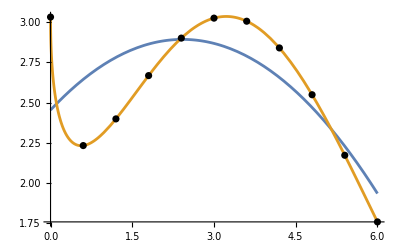

```mathematica
r=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) X⟦j⟧^(i+k)],{i,0,2}],{k,0,2}],Table[If[i==0,∑_(j=1)^(n+1) Y⟦j⟧,∑_(j=1)^(n+1) Y⟦j⟧ X⟦j⟧^i],{i,0,2}]];Q2[x_]=r.{1,x,x^2}
Show[Plot[{Q2[x], f[x]},{x,0,6}],ListPlot[data, PlotStyle->{Black}]]
```

### в) найти многочлены наилучшего среднеквадратичного приближения третьей и четвертой степеней с помощью функции Fit пакета Mathematica, проиллюстрировать графически;

2.77967-0.500976 x+0.302789 x^2-0.0419793 x^3

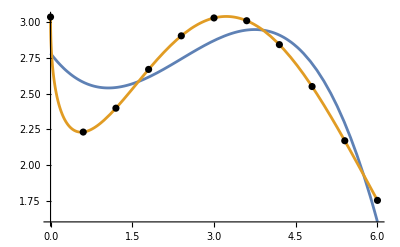

```mathematica
Q3=Fit[data,{1,x,x^2,x^3},x]
Show[Plot[{Q3, f[x]},{x,0,6}],ListPlot[data, PlotStyle->{Black}]]
```

2.96666-1.58311 x+1.20456 x^2-0.282453 x^3+0.0200394 x^4

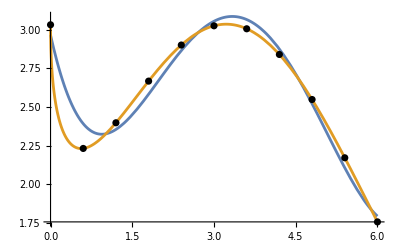

```mathematica
Q4=Fit[data,{1,x,x^2,x^3,x^4},x]
Show[Plot[{Q4, f[x]},{x,0,6}],ListPlot[data, PlotStyle->{Black}]]
```

### д) сравнить результаты, полученные в пунктах а, б и в, изобразив на одном чертеже точки (x_i,f(x_i))и графики функций Q_1(x), Q_2(x) , Q_3(x) и Q_4(x).

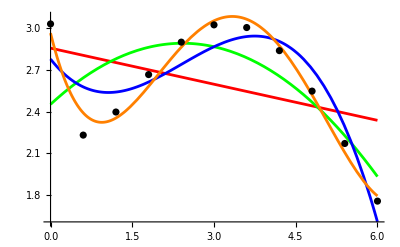

```mathematica
Show[Plot[{Q1[x],Q2[x],Q3,Q4},{x,0,6}, PlotStyle->{Red,Green,Blue,Orange}],ListPlot[data, PlotStyle->{Black}]]
```